```mathematica
DSolve[{b''[t]+(1+0.1 Sin[2t])^2b[t]==1/b[t]^4,b[0]==1,b'[0]==0},b[t],t]
```

DSolve[{b[t] (1+0.1 Sin[2 t])^2+b''[t]==1/b[t]^4,b[0]==1,b'[0]==0},b[t],t]

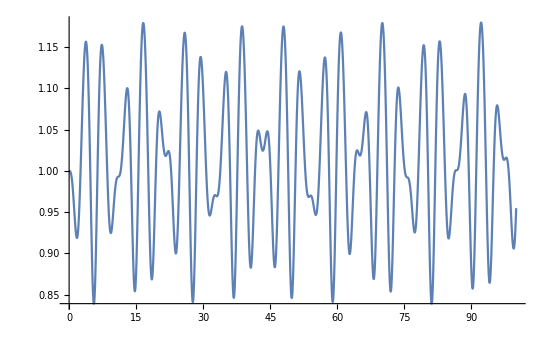

```mathematica
s=NDSolve[{b''[t]+(1+0.1Sin[√2 t])^2b[t]==1/b[t]^3,b[0]==1,b'[0]==0},b[t],{t,0,100}];
Plot[Evaluate[b[t]/.s],{t,0,100},PlotRange->All]
```

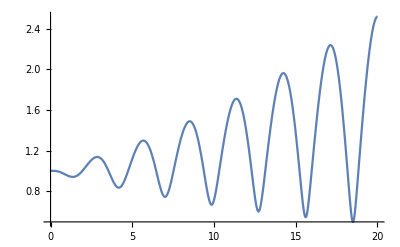

```mathematica
s1=NDSolve[{c''[t]+(1+0.1Sin[√5 t])^2c[t]==1/c[t]^4,c[0]==1,c'[0]==0},c[t],{t,0,500}];
Plot[Evaluate[c[t]/.s1],{t,0,20},PlotRange->All]
```